fk

0.

2

1.11022×10^-16

128.

Начальная точка: {-3,3}

Точность: 0.001

Количество итераций: 2

Количество вычислений функции:574

Точка минимума {1.,1.}

Значение ф-ии: 0.

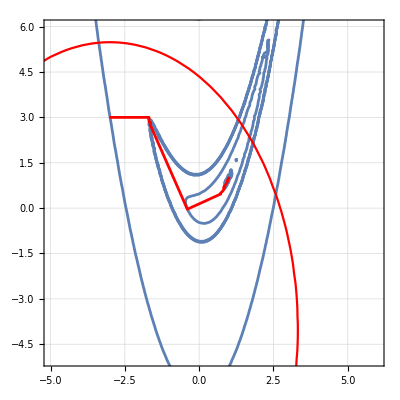

```mathematica
ClearAll;
α=5.;
(*F[{x_,y_}]:=6 x^2-4x*y+3 y^2+4*√5(x+2y)+22;*)
F[{x_,y_}]:=α*(x^2-y)^2+(x-1)^2; 
g1[x_]:=0.5*(Abs[-x]-x);
g2[x_]:=0.5*(Abs[-x]-x);
g3[{x_,y_}]:=0.5*(Abs[x+y-1]+ x+y-1);
g4[{x_,y_}]:=0.5*(Abs[(x+3)^2/4+(y+4)^2/9-10]+(x+3)^2/4+(y+4)^2/9-10);
(*g=ListLinePlot[{{0,0},{0,10},{10,0},{0,0}},PlotStyle->Red];*)
g=ContourPlot[(x+3)^2/4+(y+4)^2/9==10,{x,-10,10},{y,-10,10},ContourStyle->Red];
rk=2.;
(*fk[{x_,y_}]:=F[{x,y}]+rk*(g1[x]+g2[y]+g3[{x,y}]);*)
fk[{x_,y_}]:=F[{x,y}]+rk*(g4[{x,y}]);
rk=32.;
fk
F[{1,1}]
ϵ=10^-3;
x0={-3,3};
xk=x0;
xkn=xk;
x1={1,1};
res={};
i=0;
AppendTo[res,xk];
u={{1. ,0.},{0. , 1.}};
κ=0.5;
countf=0;
While[Norm@(fk[x1]-fk[xkn])>ϵ,{
i++;
x1=xkn;
u={{1. ,0.},{0. , 1.}};
countf++;
      
xs=x1; 
For[j=1,j<= 2,j++,{
xk=xkn;
a=-10.;
b=10.;
ak=a;
bk=b;
x1k=ak+2/(3+√5)(bk-ak);
x2k=ak+(2(bk-ak))/(1+√5);
f1=fk[xk+x1k*u[[j]]];
f2=fk[xk+x2k*u[[j]]];

While[Abs[bk-ak]>ϵ/10,
{
countf=countf+1;
If[f1<f2,{
bk=x2k;
x2k=x1k;
x1k=ak+bk-x2k;
f2=f1;
f1=fk[xk+x1k*u[[j]]];
},{
ak=x1k;
x1k=x2k;
x2k=ak+bk-x1k;
f1=f2;
f2=fk[xk+x2k*u[[j]]];
}];
}];
xkn=xk+(ak+bk)/2*u[[j]];

AppendTo[res,xkn];}];
u=Orthogonalize[{xkn-xs,u[[2]]}];
While[Norm[xs-xkn] >ϵ,{

(*i=i+1;*)
xs=xkn;
For[j=1,j<= 2,j++,{
xk=xkn;
a=-10.;
b=10.;
ak=a;
bk=b;
x1k=ak+2/(3+√5)(bk-ak);
x2k=ak+(2(bk-ak))/(1+√5);
f1=fk[xk+x1k*u[[j]]];
f2=fk[xk+x2k*u[[j]]];

While[Abs[bk-ak]>ϵ/10,
{
countf=countf+1;
If[f1<f2,{
bk=x2k;
x2k=x1k;
x1k=ak+bk-x2k;
f2=f1;
f1=fk[xk+x1k*u[[j]]];
},{
ak=x1k;
x1k=x2k;
x2k=ak+bk-x1k;
f1=f2;
f2=fk[xk+x2k*u[[j]]];
}];
}];
xkn=xk+(ak+bk)/2*u[[j]];
AppendTo[res,xkn];

}];
u=Orthogonalize[{xkn-xs,u[[2]]}];
(*u[[1]]=xkn-xs;
u[[2]]=u[[2]]-(u[[2]].u[[1]])*u[[1]];
    u[[1]]=u[[1]]/Norm@u[[1]]; 
  u[[2]]=u[[2]]/Norm@u[[2]];*)

}];
rk=rk*2;

}];
i
u[[1]].u[[2]]
fun=Map[F,res];
rk
gr={};
For[k=1,k<= Length[fun],k++,{
AppendTo[gr,ContourPlot[F[{x,y}]==fun[[k]],{x,-10,10},{y,-10,10},ContourStyle->{Thickness[0.005]},GridLines->Automatic,PlotRange->Automatic]]}];
gr12= ListLinePlot[res,PlotRange->Full,PlotStyle->{Red,Thickness[0.005]}, PlotMarkers->{Automatic,2},GridLines->Automatic,PlotRange->All,AspectRatio->1];
Print["Начальная точка: ", x0]
Print["Точность: ", N@ϵ]
Print["Количество итераций: ", i]
Print["Количество вычислений функции:", countf]
Print["Точка минимума ", N@Round[xk,ϵ]]
Print["Значение ф-ии: ",  N@Round[F[xk],ϵ]]
Show[gr, gr12,g,PlotRange->{{-5,6},{-5,6}}]
```